Plot (curvilinearPolarFig1.eps) that shows a 2d vector in polar coordinates, the radial vector,  and the angle relative to the horizon.

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

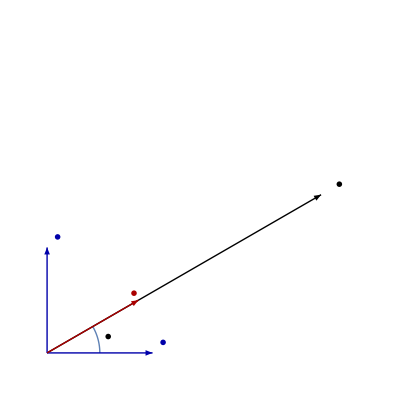

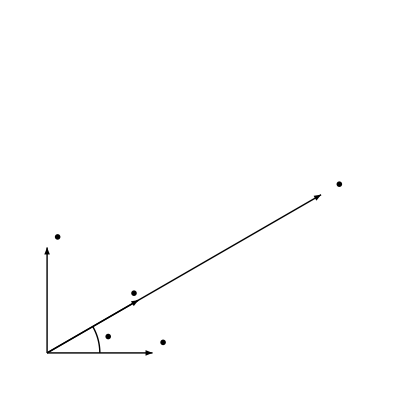

```mathematica
ClearAll[o, e1,e2, rcap, fs, bold, esub, tcap, curvilinearPolarFig1, bwcurvilinearPolarFig1, f, g]
o = {0,0};
{e1,e2} = IdentityMatrix[2];
rcap[ t_ ] := e1 Cos[t] + e2 Sin[t];
bold := MaTeX[ "\\mathbf{" <> # "}" ] &;
(*fs = MaTeX;*)
tsub[t_,s_] := MaTeX["\\mathbf{"<> t<>"}_{"<> s<>"}"]
esub[s_] := tsub["e", ToString[s]] ;
esub[s_, c_] := MaTeX["\\color{"<> c <>"}\\mathbf{e}_{"<> ToString[s]<>"}"]
tcap[s_] := MaTeX["\\hat{\\boldsymbol{" <> s <>"}}"];
(*bold := Style[#, Bold ] &;
fs := Style[#, FontSize -> 14] &;
esub := fs[Subscript["e" // bold, #]]&;
tcap := fs[bold[OverHat[#]]]  &;*)


curvilinearPolarFig1 = Module[{rho,theta, x, tr},
rho = 3;
tr = 0.5;
theta = Pi/6;
x = rho rcap[theta];
Show[{
ParametricPlot[ tr rcap[t], {t, 0, theta}, PlotRange -> {{-0.1,rho}, {-0.1,rho}}, PlotStyle-> Thick, Ticks ->None,
Axes -> None],
Graphics[{
Thick,
Text["\\theta" //MaTeX, 1.2 tr rcap[theta/2]],
Arrow[{o, x}],
Text[
MaTeX["\\mathbf{x} = \\rho \\hat{\\boldsymbol{\\rho}}"],
0.2 rcap[theta] + x ],
Blue//Darker,
Arrow[{o, e1}],
Arrow[{o, e2}],
Text[esub[1, "BlueDarker"], 1.1 e1 + 0.1 e2],
Text[esub[2, "BlueDarker"], 1.1 e2 + 0.1 e1],
Red//Darker,
Arrow[{o, rcap[theta]}],
Text[MaTeX["\\color{RedDarker}\\hat{\\boldsymbol{\\rho}}"], rcap[1.15 theta]]
}]
}]
]

bwcurvilinearPolarFig1 = Module[{rho,theta, x, tr},
rho = 3;
tr = 0.5;
theta = Pi/6;
x = rho rcap[theta];
Show[{
ParametricPlot[ tr rcap[t], {t, 0, theta}, PlotRange -> {{-0.1,rho}, {-0.1,rho}}, PlotStyle-> {Thick, Black}, Ticks ->None,
Axes -> None],
Graphics[{
Thick,
Text["\\theta" //MaTeX, 1.2 tr rcap[theta/2]],
Arrow[{o, x}],
Text[
MaTeX["\\mathbf{x} = \\rho \\hat{\\boldsymbol{\\rho}}"],
0.2 rcap[theta] + x ],

Arrow[{o, e1}],
Arrow[{o, e2}],
Text[esub[1], 1.1 e1 + 0.1 e2],
Text[esub[2], 1.1 e2 + 0.1 e1],

Arrow[{o, rcap[theta]}],
Text[tcap["\\rho"], rcap[1.15 theta]]
}]
}]
]
```

```mathematica
peeters`exportForLatex["color/curvilinearPolarFig1", curvilinearPolarFig1]
peeters`exportForLatex["bw/curvilinearPolarFig1", bwcurvilinearPolarFig1]
```

{color/curvilinearPolarFig1.eps,color/curvilinearPolarFig1pn.png}

{bw/curvilinearPolarFig1.eps,bw/curvilinearPolarFig1pn.png}